```mathematica
(*  Lewis John Lloyd
	18APR2011
*)
```

```mathematica
Quit[]
```

```mathematica
Zero = 10^-10;
TimeFinal=200;
kGraphite=60;(*[W/m-K]*)
SpecificHeatGraphite =710;(* [J/kg-K]*)
DensityGraphite=2267; (*[kg/m^3]*)
DiameterPebble = 0.06; (*[m]*)
DiameterFuel = 0.05; (*[m]*)
RadiusPebble=0.5*DiameterPebble; (*[m]*)
RadiusFuel=0.5*DiameterFuel;(*[m]*)
VolumePebble = 4/3 π RadiusPebble^3;(*[m^3]*)
VolumeFuel=4/3 π RadiusFuel^3;(*[m^3]*)
SurfacePebble=4π RadiusPebble^2;(*[m^2]*)
CharacteristicRadius=VolumePebble/SurfacePebble;(*[m]*)
TemperatureBulk=800;(*[K]*)
HeatTransferCoefficient=500;(*[W/m^2-K]*)
VolumetricHeatSourceInitial=30 10^6;(*[W/m^3]*)

VolumetricHeatSource[t_,r_]=VolumetricHeatSourceInitial(1.5-0.5 ⅇ^(-0.04 t))*(HeavisideTheta[r+Zero]-HeavisideTheta[r-RadiusFuel])*HeavisideTheta[t+Zero];(*[W/m^3*)

TempInner[r_]=Limit[Limit[T[r]/.DSolve[1/r^2 D[r^2 kGraphite D[T[r],r],r]==-VolumetricHeatSourceInitial,T[r],r],C[1]->A0][[1]],C[2]->B0];
TempOuter[r_]=Limit[Limit[T[r]/.DSolve[1/r^2 D[r^2 kGraphite D[T[r],r],r]==0,T[r],r],C[1]->A1][[1]],C[2]->B1];
EquationConstants={A0,A1,B0,B1}/.Solve[{Limit[r^2 TempInner'[r],r->-Zero]==0,
TempInner[RadiusFuel]==TempOuter[RadiusFuel],
-kGraphite TempInner'[RadiusFuel]==-kGraphite TempOuter'[RadiusFuel],
-kGraphite TempOuter'[RadiusPebble]==HeatTransferCoefficient(TempOuter[RadiusPebble]-TemperatureBulk)
},{A0,A1,B0,B1}][[1]]//Expand//Simplify//Chop;
TemperatureInitial[r_]=(Limit[Limit[TempInner[r],A0->EquationConstants[[1]]],B0->EquationConstants[[3]]])*(HeavisideTheta[r+Zero]-HeavisideTheta[r-RadiusFuel])+(Limit[Limit[TempOuter[r],A1->EquationConstants[[2]]],B1->EquationConstants[[4]]])*(HeavisideTheta[r-RadiusFuel]-HeavisideTheta[r-RadiusPebble]);
test[t_,r_]=Temp[t,r]/.NDSolve[{
DensityGraphite SpecificHeatGraphite D[Temp[t,r], t]==kGraphite/r^2 D[(r^2 D[Temp[t,r], r]), r]+VolumetricHeatSource[t,r],
-kGraphite Derivative[0,1][Temp][t,Zero] ==0,
-kGraphite Derivative[0,1][Temp][t,RadiusPebble] ==HeatTransferCoefficient(Temp[t,RadiusPebble]-TemperatureBulk),
Temp[Zero,r] ==TemperatureInitial[r]
},{Temp},{r,Zero,RadiusPebble},{t,0,TimeFinal}][[1]];
TemperatureAverage = Integrate[TemperatureInitial[r] r^2,{r,Zero,RadiusPebble}]/Integrate[r^2,{r,Zero,RadiusPebble}];
ThetaInitialAnalytic=TemperatureAverage-TemperatureBulk;
ThetaInitialNumeric = NIntegrate[(test[Zero,r])r^2,{r,Zero,RadiusPebble}]/Integrate[r^2,{r,Zero,RadiusPebble}]-TemperatureBulk;
HeatSource[t_]=VolumetricHeatSource[t,0]*VolumeFuel;
TauPebble = (HeatTransferCoefficient SurfacePebble)/(DensityGraphite SpecificHeatGraphite VolumePebble) ;(*[1/s]*) 
ThetaAnalytic[t_]=(TempDiff[t]/.DSolve[{D[TempDiff[t],t]==-TauPebble TempDiff[t]+HeatSource[t]/(DensityGraphite SpecificHeatGraphite VolumePebble),
TempDiff[0]==ThetaInitialAnalytic},TempDiff[t],t][[1]])/ThetaInitialAnalytic//FullSimplify;
ThetaNumeric[t_]:=(NIntegrate[(test[t,r])r^2,{r,Zero,RadiusPebble}]/Integrate[r^2,{r,Zero,RadiusPebble}]-TemperatureBulk)/ThetaInitialNumeric;
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable r.

NDSolve::ibcinc: Warning: Boundary and initial conditions are inconsistent.

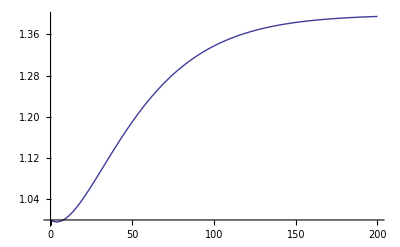

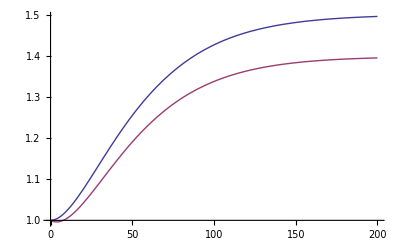

```mathematica
Plot[ThetaAnalytic[t],{t,0,TimeFinal}]
Plot[{ThetaNumeric[t],ThetaAnalytic[t]},{t,0,TimeFinal}]
```

```mathematica
ListAnimate[Table[Plot[test[t/10,r],{r,Zero,RadiusPebble},PlotRange->{1100,1500}],{t,1000}]]
```